# Tecnológico de Monterrey Campus Toluca

## Métodos numéricos: Segundo Examen Parcial

Nombre y Matrícula: Mario Jacob García Navarro - A01363206

Datos: Fecha: 27 de junio 2014; Grupo 01; Semestre: Verano 2014

Instrucciones:

Se calificará el orden, limpieza y desarrollo lógico de tus respuestas.

## Métodos de Aproximación de Raíces

Aplica los algoritmos de Bisección, Secante y Newton Raphson, para aproximar el cero de la función f(x)=3 ⅇ^x-4Cos(x) en el intervalo [0.1,1]. Para el método de la secante proponga P_0, P_(1,) y para Newton Raphson, X_0. Con todo lo anterior, construya una única tabla donde se reflejen los resultados y los errores.

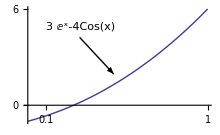

### Módulo de Bisección

```mathematica
Biseccion[a0_,b0_,m_] :=
Module[{},
a = N[a0];  
b = N[b0];  
c = (a + b)/2; 
k = 0; 
output={{k,a,c,b,f[c]}}; 
While[k < m,
If[ Sign[f[b]] ==  Sign[f[c]], 
b = c, a = c; ]; 
c = (a + b)/2; 
k = k+1; 
output=Append[output,{k,a,c,b,f[c]}]; ]; 
Print[NumberForm[TableForm[output,
TableHeadings->{None,{"k","a_k","c_k","b_k","f[c_k]"}}],16]]; 
Print["  c  = ",NumberForm[c,16] ]; 
Print[" Δc  = ±",(b-a)/2]; 
Print["f[c] = ",NumberForm[f[c],16] ]; ]
```

### Módulo de Secante

```mathematica
Secante[x0_,x1_,max_]:=
Module[{},
k = 1; 
p0 = N[x0]; 
p1 = N[x1]; 
Print["f[x] = ",f[x] ];
Print["p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])"]; 
Print["p_0 = ",PaddedForm[p0,{16,16}],",   f[p_0] = ",NumberForm[f[p0],16] ]; 
Print["p_1 = ",PaddedForm[p1,{16,16}],",   f[p_1] = ",NumberForm[f[p1],16] ];  
p2 = p1; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p2; 
p2 = p1 - (f[p1](p1 - p0))/(f[p1] - f[p0]); 
k = k+1; 
Print[Subscript["p", k]," = ",PaddedForm[p2,{16,16}],",   f[",Subscript["p", k],"] = ",NumberForm[f[p2],16] ]; ]; 
Print[""]; 
Print["f[x] = ",f[x] ];
Print["  p  = ",NumberForm[p2,16] ]; 
Print[" Δp  = ±",Abs[p2-p1] ]; 
Print["f[p] = ",NumberForm[f[p2],16] ]; ]
```

### Módulo de Newton Raphson

```mathematica
NewtonRaphson[x0_,max_]:=
Module[{},
k = 0; 
p0 = N[x0]; 
Print["f[x] = ",f[x] ];
g[x_]=x-f[x]/f'[x]; 
Print["g[x] = x - f[x]/f'[x]"]; 
Print["g[x] = ",g[x] ];
Print["g[x] = ",Simplify[g[x]]];
Print["  p_0 = ",PaddedForm[p0,{16,16}],",   f[p_0] = ",NumberForm[f[p0],16] ]; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p0 - f[p0]/f'[p0]; 
k = k+1;  
Print[Subscript["  p", k]," = ",PaddedForm[p1,{16,16}],",   f[",Subscript["p", k],"] = ",NumberForm[f[p1],16] ]; ]; 
Print[""]; 
Print["f[x] = ",f[x] ];
Print["  p  = ",NumberForm[p1,16] ]; 
Print[" Δp  = ±",Abs[p1-p0] ]; 
Print["f[p] = ",NumberForm[f[p1],16] ]; ]
```

### Función y Gráfica

```mathematica
f[x_]:=3 ⅇ^x-4 Cos[x];
```

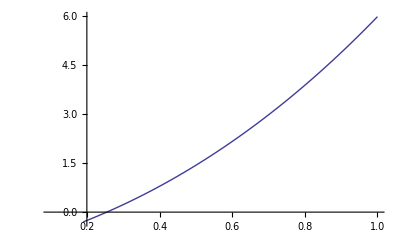

```mathematica
Plot[f[x],{x,0.1,1}, PlotRange->{{0.1,1},{-0.3,6}},AxesOrigin->Automatic]
```

NOTA: Los siguientes resultados son únicamente para documentar el proceso. La tabla única que se pide se encuentra algunas subsecciones más abajo.

#### Resultados arrojados por Método de Bisección

```mathematica
Biseccion[0.1,1,11]
```

k | a_k | c_k | b_k | f[c_k]
0 | 0.1 | 0.55 | 1. | 1.789660965364163
1 | 0.1 | 0.325 | 0.55 | 0.3614890322829911
2 | 0.1 | 0.2125 | 0.325 | -0.1997284959936674
3 | 0.2125 | 0.26875 | 0.325 | 0.06856982394377154
4 | 0.2125 | 0.240625 | 0.26875 | -0.068625095874149
5 | 0.240625 | 0.2546875000000001 | 0.26875 | -0.0007930566513505433
6 | 0.2546875000000001 | 0.26171875 | 0.26875 | 0.03369653095828173
7 | 0.2546875000000001 | 0.2582031250000001 | 0.26171875 | 0.01640383617194496
8 | 0.2546875000000001 | 0.2564453125000001 | 0.2582031250000001 | 0.007793422288516094
9 | 0.2546875000000001 | 0.25556640625 | 0.2564453125000001 | 0.003497191922330334
10 | 0.2546875000000001 | 0.255126953125 | 0.25556640625 | 0.001351320032888292
11 | 0.2546875000000001 | 0.2549072265625001 | 0.255126953125 | 0.0002789448053008847

c  = 0.2549072265625001

Δc  = ±0.000219727

f[c] = 0.0002789448053008847

#### Resultados arrojados por Método de la Secante

```mathematica
(** Se escogen los puntos Subscript[P, 0] y Subscript[P, 1] **)
```

```mathematica
PCero= 0.1;
PUno=0.5;
```

```mathematica
Secante[PCero,PUno,7]
```

f[x] = 3 ⅇ^x-4 Cos[x]

p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])

p_0 =  0.1000000000000000,   f[p_0] = -0.6645039068851601

p_1 =  0.5000000000000000,   f[p_1] = 1.435833564538894

p_2 =  0.2265518357742041,   f[p_2] = -0.134983963861933

p_3 =  0.2500498655902733,   f[p_3] = -0.02333199333765812

p_4 =  0.2549602659400586,   f[p_4] = 0.0005377692009513879

p_5 =  0.2548496380245867,   f[p_5] = -2.054165708198497×10^-6

p_6 =  0.2548500589920446,   f[p_6] = -1.795825710360077×10^-10

p_7 =  0.2548500590288503,   f[p_7] = 0.

f[x] = 3 ⅇ^x-4 Cos[x]

p  = 0.2548500590288503

Δp  = ±3.68057×10^-11

f[p] = 0.

#### Resultados arrejados por Método de NewtonRaphson

```mathematica
(** Se escoge el punto Subscript[X, 0] **)
```

```mathematica
XCero=2.5;
```

```mathematica
NewtonRaphson[XCero,7]
```

f[x] = 3 ⅇ^x-4 Cos[x]

g[x] = x - f[x]/f'[x]

g[x] = x-(3 ⅇ^x-4 Cos[x])/(3 ⅇ^x+4 Sin[x])

g[x] = x+(-3 ⅇ^x+4 Cos[x])/(3 ⅇ^x+4 Sin[x])

p_0 =  2.5000000000000000,   f[p_0] = 39.75205634429815

p_1 =  1.4791818860962970,   f[p_1] = 12.80211431012037

p_2 =  0.7327588443915304,   f[p_2] = 3.269112892026937

p_3 =  0.3661895882248135,   f[p_3] = 0.5918920283617735

p_4 =  0.2634114094478078,   f[p_4] = 0.04205660624071283

p_5 =  0.2549075478345110,   f[p_5] = 0.0002805125001077435

p_6 =  0.2548500616505636,   f[p_6] = 1.279187866742859×10^-8

p_7 =  0.2548500590288503,   f[p_7] = 0.

f[x] = 3 ⅇ^x-4 Cos[x]

p  = 0.2548500590288503

Δp  = ±2.62171×10^-9

f[p] = 0.

#### Métodos que regresan únicamente los resultados de las raíces

```mathematica
ResultadoBiseccion[a0_,b0_,m_] :=
Module[{},
a = N[a0];  
b = N[b0];  
c = (a + b)/2; 
k = 0; 
output={{k,a,c,b,f[c]}}; 
While[k < m,
If[ Sign[f[b]] ==  Sign[f[c]], 
b = c, a = c; ]; 
c = (a + b)/2; 
k = k+1; 
output=Append[output,{k,a,c,b,f[c]}]]; Return[c];];
```

```mathematica
ResultadoSecante[x0_,x1_,max_]:=
Module[{},
k = 1; 
p0 = N[x0]; 
p1 = N[x1]; 
p2 = p1; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p2; 
p2 = p1 - (f[p1](p1 - p0))/(f[p1] - f[p0]); 
k = k+1;  ]; Return[ p2] ];
```

```mathematica
ResultadosNewtonRaphson[x0_,max_]:=
Module[{},
k = 0; 
p0 = N[x0]; 
g[x_]=x-f[x]/f'[x]; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p0 - f[p0]/f'[p0]; 
k = k+1;  ]; Return[p1] ]
```

#### Métodos que regresan únicamente los errores de las aproximaciones

```mathematica
ErrorBiseccion[a0_,b0_,m_] :=
Module[{},
a = N[a0];  
b = N[b0];  
c = (a + b)/2; 
k = 0; 
output={{k,a,c,b,f[c]}}; 
While[k < m,
If[ Sign[f[b]] ==  Sign[f[c]], 
b = c, a = c; ]; 
c = (a + b)/2; 
k = k+1; 
output=Append[output,{k,a,c,b,f[c]}]]; Return[f[c]];];
```

```mathematica
ErrorSecante[x0_,x1_,max_]:=
Module[{},
k = 1; 
p0 = N[x0]; 
p1 = N[x1]; 
p2 = p1; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p2; 
p2 = p1 - (f[p1](p1 - p0))/(f[p1] - f[p0]); 
k = k+1;  ]; Return[ f[p2]] ];
```

```mathematica
ErrorNewtonRaphson[x0_,max_]:=
Module[{},
k = 0; 
p0 = N[x0]; 
g[x_]=x-f[x]/f'[x]; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p0 - f[p0]/f'[p0]; 
k = k+1;  ]; Return[f[p1]] ]
```

### Generación de la tabla única

NOTA: Se utilizaron los errores relativos a cero, es decir, la aproximación se mide dependiendo de la altura en la que se evaluó. Esto se deriva de que no hay una solución exacta o por métodos comunes. Como se puede apreciar, el sistema no puede solucionarse con los métodos disponibles de ‘Solve’. El error que se utilizó fue de tipo “Absoluto y Porcentual”-

```mathematica
Solve[3 ⅇ^x-4 Cos[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[3 ⅇ^x-4 Cos[x]==0,x]

```mathematica
TableForm[
Table[{i,ResultadoBiseccion[0.1,1,i],ResultadoSecante[PCero,PUno,i],ResultadosNewtonRaphson[XCero,i], Abs[PorcentajeBiseccion[0.1,1,i]*100],Abs[PorcentajeSecante[0PCero,PUno,i]*100],Abs[PorcentajeNewtonRaphson[XCero,i]*100]},{i,0,8}],TableHeadings->{None,{"Índice","Bisección (Resultado)", "Secante (Resultado)", "Newton Raphson (Resultado)","Bisección (Error Absoluto Porcentual)","Secante (Error Absoluto Porcentual)","Newton Raphson (Error Absoluto Porcentual)"}}]
```

Índice | Bisección (Resultado) | Secante (Resultado) | Newton Raphson (Resultado) | Bisección (Error Absoluto Porcentual) | Secante (Error Absoluto Porcentual) | Newton Raphson (Error Absoluto Porcentual)
0 | 0.55 | 0.5 | 2.5 | 178.966 | 143.583 | 3975.21
1 | 0.325 | 0.5 | 1.47918 | 36.1489 | 143.583 | 1280.21
2 | 0.2125 | 0.226552 | 0.732759 | 19.9728 | 23.2461 | 326.911
3 | 0.26875 | 0.25005 | 0.36619 | 6.85698 | 4.12589 | 59.1892
4 | 0.240625 | 0.25496 | 0.263411 | 6.86251 | 0.170055 | 4.20566
5 | 0.254688 | 0.25485 | 0.254908 | 0.0793057 | 0.00115454 | 0.0280513
6 | 0.261719 | 0.25485 | 0.25485 | 3.36965 | 3.19067×10^-7 | 1.27919×10^-6
7 | 0.258203 | 0.25485 | 0.25485 | 1.64038 | 6.66134×10^-13 | 0.
8 | 0.256445 | 0.25485 | 0.25485 | 0.779342 | 0. | 0.

## Matrices

Utilizando al menos una  matriz de homotecia,  generar el siguiente “Manipulate”:

-Graphics-

### Triángulo Isósceles

```mathematica
triangulo={{0,0},{1,0},{0.5,1},{0,0}}
```

{{0,0},{1,0},{0.5,1},{0,0}}

```mathematica
Manipulate[
Graphics[Line[{triangulo,Flatten[Table[Flatten[Table[Transpose[({{0.0625 j 2, 0}, {0, 0.0625 j 2}}).({{triangulo[[i,1]]}, {triangulo[[i,2]]}})+({{0.46-(j*3-1)/50}, {0.46-(j*3-1)/50}})],{i,Length[triangulo]}],1],{j,k}],1]}]],{k,0,15,1}]
```

### Comparación con la imágen que se quiere lograr

-Graphics-

### Triángulo Equilatero

```mathematica
equilatero={{0,0},{1,0},{0.5,0.5},{0,0}}
```

{{0,0},{1,0},{0.5,0.5},{0,0}}

```mathematica
Manipulate[
Graphics[Line[{equi,Flatten[Table[Flatten[Table[Transpose[({{0.0625 j 2, 0}, {0, 0.0625 j 2}}).({{equi[[i,1]]}, {equi[[i,2]]}})+({{0.465-(j*3-1)/50}, {0.23-(j*3-1)/100}})],{i,Length[equi]}],1],{j,k}],1]}]],{k,0,15,1}]
```